# Transfer Function for Dark Matter

```mathematica
ClearAll["Global`*"]
```

## BBKS Transfer Function -

```mathematica
T[x_]:=SetPrecision[Log[1+0.171*x]/(0.171*x)*(1+0.284*x+(1.18*x)^2+(0.399*x)^3+(0.490*x)^4)^(-0.25),50]
rangeX=Join[Subdivide[0.01,10.,200],Subdivide[10.+0.01,1000.,100]];
TBBKS=Table[T[x],{x,rangeX}];
```

## sCDM Linear Perturbation Equations

### [sCDM] Evolution of the (normalized) gravitational potential for different values of

```mathematica
c=299792.458;
ΩΛ=0.;
Ωm=1.-ΩΛ;
h=0.5;
H0=100.*h*1/c;
aeq=(4.15*10^(-5))/(Ωm*h^2);
keqs=0.073*Ωm*h^2;
ai=N[10^(-8)];
af=1.;
H2[a_]:=H0^2*Ωm*(aeq*a^(-4)+a^(-3)+ΩΛ/Ωm)
Ht[a_]:=a*Sqrt[H2[a]]
y[a_]:=a/aeq
```

```mathematica
sCDM=ParametricNDSolve[
{a*Ht[a]*Θr0'[a]+k*Θr1[a]==-a*Ht[a]*Φ'[a],
a*Ht[a]*Θr1'[a]-k/3.*Θr0[a]==-k/3.*Φ[a],
a*Ht[a]*δ'[a]-k*v[a]==-3.*a*Ht[a]*Φ'[a],
a*Ht[a]*v'[a]+Ht[a]*v[a]==k*Φ[a],
k^2*Φ[a]+3.*Ht[a]*(a*Ht[a]*Φ'[a]+Ht[a]*Φ[a])==1.5*Ht[a]^2*y[a]/(1.+y[a]*(1+ΩΛ/Ωm*a^3))*(δ[a]+4./y[a]*Θr0[a]),
Φ[ai]==2.*Θr0[ai],δ[ai]==3.*Θr0[ai],v[ai]==k/(2.*Ht[ai])*Φ[ai],Θr1[ai]==-k/(6.*Ht[ai])*Φ[ai],Θr0[ai]==0.5
},
{Θr0,Θr1,Φ,δ,v},{a,ai,af},{k}]
```

{Θr0→ParametricFunction[<>],Θr1→ParametricFunction[<>],Φ→ParametricFunction[<>],δ→ParametricFunction[<>],v→ParametricFunction[<>]}

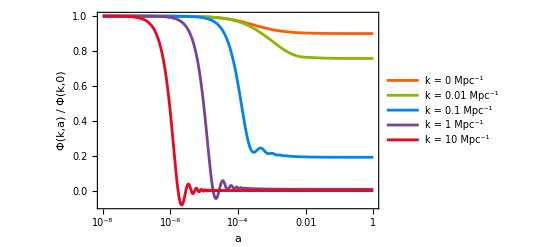

```mathematica
plt1=LogLinearPlot[{Evaluate[Φ[0.][a]/.sCDM],Evaluate[Φ[0.01][a]/.sCDM],Evaluate[Φ[0.1][a]/.sCDM],Evaluate[Φ[1.][a]/.sCDM],Evaluate[Φ[10.][a]/.sCDM]},{a,ai,af},
PlotRange->All,
PlotStyle->{ColorData[3][2],ColorData[3][4],ColorData[3][6],ColorData[3][8],ColorData[3][10]},
PlotLegends->Placed[{
Row[{"k = 0 ",Superscript["Mpc","-1"]}],
Row[{"k = 0.01 ",Superscript["Mpc","-1"]}],
Row[{"k = 0.1 ",Superscript["Mpc","-1"]}],
Row[{"k = 1 ",Superscript["Mpc","-1"]}],
Row[{"k = 10 ",Superscript["Mpc","-1"]}]
},After],
LabelStyle->Directive[FontSize->13],AxesStyle->Thickness[0.005],Frame->True,FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->{Style["a",Bold],Style["Φ(k,a) / Φ(k,0)",Bold]},GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed]]
```

### [sCDM] Transfer Function

```mathematica
c=299792.458;
ΩΛ=0.;
Ωm=1.-ΩΛ;
h=0.5;
H0=100.*h*1/c;
aeq=(4.15*10^(-5))/(Ωm*h^2);
keqs=0.073*Ωm*h^2;
ai=N[10^(-8)];
af=0.1;
H2[a_]:=H0^2*Ωm*(aeq*a^(-4)+a^(-3)+ΩΛ/Ωm)
Ht[a_]:=a*Sqrt[H2[a]]
y[a_]:=a/aeq
```

```mathematica
sCDM=ParametricNDSolve[
{a*Ht[a]*Θr0'[a]+k*Θr1[a]==-a*Ht[a]*Φ'[a],
a*Ht[a]*Θr1'[a]-k/3.*Θr0[a]==-k/3.*Φ[a],
a*Ht[a]*δ'[a]-k*v[a]==-3.*a*Ht[a]*Φ'[a],
a*Ht[a]*v'[a]+Ht[a]*v[a]==k*Φ[a],
k^2*Φ[a]+3.*Ht[a]*(a*Ht[a]*Φ'[a]+Ht[a]*Φ[a])==1.5*Ht[a]^2*y[a]/(1.+y[a]*(1+ΩΛ/Ωm*a^3))*(δ[a]+4./y[a]*Θr0[a]),
Φ[ai]==2.*Θr0[ai],δ[ai]==3.*Θr0[ai],v[ai]==k/(2.*Ht[ai])*Φ[ai],Θr1[ai]==-k/(6.*Ht[ai])*Φ[ai],Θr0[ai]==0.5
},
{Θr0,Θr1,Φ,δ,v},{a,ai,af},{k}]
```

{Θr0→ParametricFunction[<>],Θr1→ParametricFunction[<>],Φ→ParametricFunction[<>],δ→ParametricFunction[<>],v→ParametricFunction[<>]}

```mathematica
TsCDM=Table[Evaluate[Φ[x*keqs][0.1]/.sCDM]/Evaluate[Φ[0.][0.1]/.sCDM],{x,rangeX}];
```

## CDM Linear Perturbation Equations

### [CDM] Evolution of the (normalized) gravitational potential for different values of

```mathematica
c=299792.458;
ΩΛ=0.7;
Ωm=1.-ΩΛ;
h=0.7;
H0=100*h*1/c;
aeq=(4.15*10^(-5))/(Ωm*h^2);
keqΛ=0.073*Ωm*h^2;
ai=N[10^(-8)];
af=1.;
H2[a_]:=H0^2*Ωm*(aeq*a^(-4)+a^(-3)+ΩΛ/Ωm)
Ht[a_]:=a*Sqrt[H2[a]]
y[a_]:=a/aeq
```

```mathematica
ΛCDM=ParametricNDSolve[
{a*Ht[a]*Θr0'[a]+k*Θr1[a]==-a*Ht[a]*Φ'[a],
a*Ht[a]*Θr1'[a]-k/3.*Θr0[a]==-k/3.*Φ[a],
a*Ht[a]*δ'[a]-k*v[a]==-3.*a*Ht[a]*Φ'[a],
a*Ht[a]*v'[a]+Ht[a]*v[a]==k*Φ[a],
k^2*Φ[a]+3.*Ht[a]*(a*Ht[a]*Φ'[a]+Ht[a]*Φ[a])==1.5*Ht[a]^2*y[a]/(1.+y[a]*(1+ΩΛ/Ωm*a^3))*(δ[a]+4./y[a]*Θr0[a]),
Φ[ai]==2.*Θr0[ai],δ[ai]==3.*Θr0[ai],v[ai]==k/(2.*Ht[ai])*Φ[ai],Θr1[ai]==-k/(6.*Ht[ai])*Φ[ai],Θr0[ai]==0.5
},
{Θr0,Θr1,Φ,δ,v},{a,ai,af},{k}]
```

{Θr0→ParametricFunction[<>],Θr1→ParametricFunction[<>],Φ→ParametricFunction[<>],δ→ParametricFunction[<>],v→ParametricFunction[<>]}

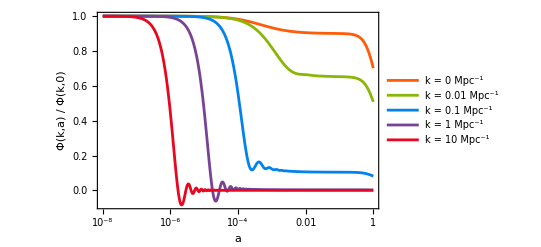

```mathematica
plt2=LogLinearPlot[{Evaluate[Φ[0.][a]/.ΛCDM],Evaluate[Φ[0.01][a]/.ΛCDM],Evaluate[Φ[0.1][a]/.ΛCDM],Evaluate[Φ[1.][a]/.ΛCDM],Evaluate[Φ[10.][a]/.ΛCDM]},{a,ai,af},
PlotRange->All,
PlotStyle->{ColorData[3][2],ColorData[3][4],ColorData[3][6],ColorData[3][8],ColorData[3][10]},
PlotLegends->Placed[{
Row[{"k = 0 ",Superscript["Mpc","-1"]}],
Row[{"k = 0.01 ",Superscript["Mpc","-1"]}],
Row[{"k = 0.1 ",Superscript["Mpc","-1"]}],
Row[{"k = 1 ",Superscript["Mpc","-1"]}],
Row[{"k = 10 ",Superscript["Mpc","-1"]}]
},After],
LabelStyle->Directive[FontSize->13],AxesStyle->Thickness[0.005],Frame->True,FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->{Style["a",Bold],Style["Φ(k,a) / Φ(k,0)",Bold]},GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed]]
```

### [CDM] Transfer Function

```mathematica
c=299792.458;
ΩΛ=0.7;
Ωm=1.-ΩΛ;
h=0.7;
H0=100*h*1/c;
aeq=(4.15*10^(-5))/(Ωm*h^2);
keqΛ=0.073*Ωm*h^2;
ai=N[10^(-8)];
af=0.1;
H2[a_]:=H0^2*Ωm*(aeq*a^(-4)+a^(-3)+ΩΛ/Ωm)
Ht[a_]:=a*Sqrt[H2[a]]
y[a_]:=a/aeq
```

```mathematica
ΛCDM=ParametricNDSolve[
{a*Ht[a]*Θr0'[a]+k*Θr1[a]==-a*Ht[a]*Φ'[a],
a*Ht[a]*Θr1'[a]-k/3.*Θr0[a]==-k/3.*Φ[a],
a*Ht[a]*δ'[a]-k*v[a]==-3.*a*Ht[a]*Φ'[a],
a*Ht[a]*v'[a]+Ht[a]*v[a]==k*Φ[a],
k^2*Φ[a]+3.*Ht[a]*(a*Ht[a]*Φ'[a]+Ht[a]*Φ[a])==1.5*Ht[a]^2*y[a]/(1.+y[a]*(1+ΩΛ/Ωm*a^3))*(δ[a]+4./y[a]*Θr0[a]),
Φ[ai]==2.*Θr0[ai],δ[ai]==3.*Θr0[ai],v[ai]==k/(2.*Ht[ai])*Φ[ai],Θr1[ai]==-k/(6.*Ht[ai])*Φ[ai],Θr0[ai]==0.5
},
{Θr0,Θr1,Φ,δ,v},{a,ai,af},{k}]
```

{Θr0→ParametricFunction[<>],Θr1→ParametricFunction[<>],Φ→ParametricFunction[<>],δ→ParametricFunction[<>],v→ParametricFunction[<>]}

```mathematica
TΛCDM=Table[Evaluate[Φ[x*keqΛ][0.1]/.ΛCDM]/Evaluate[Φ[0.][0.1]/.ΛCDM],{x,rangeX}];
```

## Comparison between sCDM and CDM Transfer Function with BBKS Transfer Function

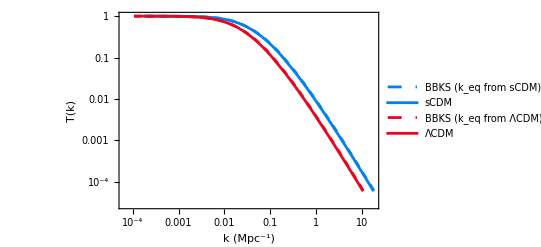

```mathematica
plt3=ListLogLogPlot[{Transpose[{rangeX*keqs,TBBKS}],Transpose[{rangeX*keqs,TsCDM}],Transpose[{rangeX*keqΛ,TBBKS}],Transpose[{rangeX*keqΛ,TΛCDM}]},
Joined->True,PlotRange->All,
PlotStyle->{{Dashed,ColorData[3][6]},ColorData[3][6],{Dashed,ColorData[3][10]},ColorData[3][10]},
PlotLegends->Placed[{
Row[{"BBKS (",Subscript["k","eq"]," from sCDM)"}],
Row[{"sCDM"}],
Row[{"BBKS (",Subscript["k","eq"]," from ΛCDM)"}],
Row[{"ΛCDM"}]
},After],
LabelStyle->Directive[FontSize->13],AxesStyle->Thickness[0.005],Frame->True,FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->{Style[Row[{"k (",Superscript["Mpc","-1"],")"}],Bold],Style["T(k)",Bold]},GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed]]
```